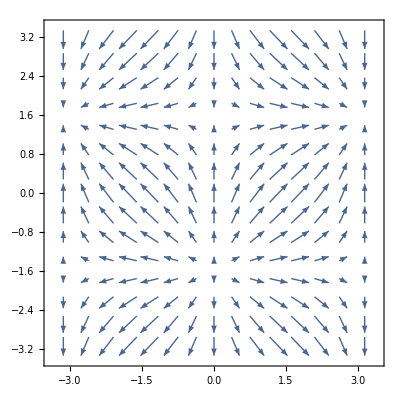

```mathematica
VectorPlot[{Sin[x],Cos[y]},{x,-Pi,Pi},{y,-Pi,Pi},VectorScale->Small]
```

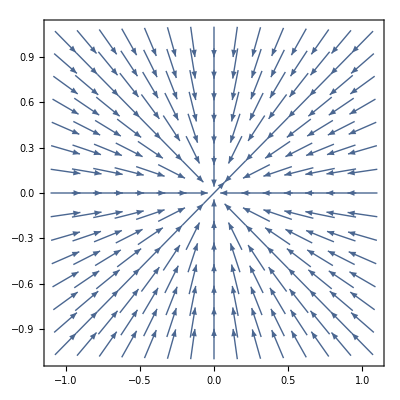
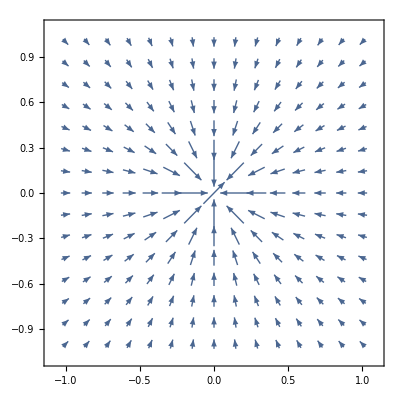

```mathematica
VectorPlot[{-(x/(x^2+y^2)^(3/2)),-(y/(x^2+y^2)^(3/2))},{x,-1,1},{y,-1,1},VectorScale->{Automatic,Automatic,#}]&/@{None,Function[If[#5>50,None,#5^.3]]}
```

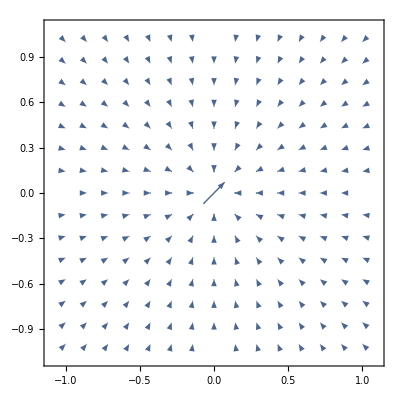

```mathematica
VectorPlot[{-(x/(x^2+y^2)^(3/2)),-(y/(x^2+y^2)^(3/2))},{x,-1,1},{y,-1,1},VectorScale->{Automatic,Automatic,Function[Log[#5]]}]
```

```mathematica
VectorPlot[{-Log[1/(x^2+y^2)]*(x/(x^2+y^2)^(1/2)),-Log[1/(x^2+y^2)]*(y/(x^2+y^2)^(1/2))},{x,-1,1},{y,-1,1}]
```